## ^183Au - Wobbling Motion

### Theoretical results → Numerical Implementation

```mathematica
ClearAll["Global*`"]
```

### Odd-particles & other functions

```mathematica
j1=N[13/2];
I01=N[13/2];
j2=N[9/2];
I02=N[9/2];
IF[MOI_]:=1/(2*MOI);
RAD[angle_]:=angle*π/180;
```

```mathematica
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)(I+j)/2+A1*(I-j)^2-V*(2j-1)/(j+1)*Sin[γ+π/6];
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-1*(((2I-1)*(A3-A1)+2j*A1)*((2I-1)*(A2-A1)+2j*A1)+8*A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=((((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))-4I*j*A3^2)*(((2I-1)*(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ])-4I*j*A2^2));
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]-Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]+Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Energy[nw1_,nw2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](nw1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](nw2+1/2);
ExcEn[nw1_,nw2_,I0_,I_,j_,A1_,A2_,A3_,V_,γ_]:=Energy[nw1,nw2,I,j,A1,A2,A3,V,γ]-Energy[0,0,I0,j,A1,A2,A3,V,γ];
band1Plus[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[0,0,I01,I,j1,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
band2Plus[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[1,0,I01,I,j1,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
```

## Experimental data

## ^183Au

#### Positive Parity Bands

```mathematica
s1Plus=Table[N[i],{i,6.5,32.5,2}];
s2Plus=Table[N[i],{i,11.5,21.5,2}];
yrastPlus=N[{702,867,1151,1530,1983,2492,3049,3655,4308,4986,5677,6375,7103,7848}/1000];
tw1Plus=N[{1739,2178,2684,3243,3840,4464}/1000];
e0=yrastPlus[[1]];
yrastPlus=Table[yrastPlus[[i]]-e0,{i,1,Length[yrastPlus]}];
tw1Plus=Table[tw1Plus[[i]]-e0,{i,1,Length[tw1Plus]}];
```

```mathematica
chi2FuncPlus[I1_,I2_,I3_,V_,γ_]:=If[Im[Sqrt[1/(Length[s1Plus]+Length[s2Plus]+1)(Sum[(yrastPlus[[i]]-band1Plus[s1Plus[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Plus]}]+Sum[(tw1Plus[[i]]-band2Plus[s2Plus[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Plus]}])]]==0,Sqrt[1/(Length[s1Plus]+Length[s2Plus]+1)(Sum[(yrastPlus[[i]]-band1Plus[s1Plus[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s1Plus]}]+Sum[(tw1Plus[[i]]-band2Plus[s2Plus[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[s2Plus]}])],10^7];
minChi2Plus=NMinimize[{chi2Func[I1,I2,I3,V,γ],1≤I1≤90&&1≤I2≤90&&1≤I3≤90&&0.01≤V≤10.0&&19≤γ≤25},{I1,I2,I3,V,γ}];
paramSetPlus=Values@minChi2Plus[[2]];
rmsValuePLus=minChi2Plus[[1]];
Print[paramSetPlus]
Print[rmsValuePLus]
```

{83.4294,3.64419,25.7625,1.99236,19.}

0.0735616

```mathematica
Print["********** BAND 1 - POSITIVE PARITY **********"]
Do[Print[s1Plus[[i]]," ",yrastPlus[[i]]," ",band1Plus[s1Plus[[i]],paramSetPlus[[1]],paramSetPlus[[2]],paramSetPlus[[3]],paramSetPlus[[4]],paramSetPlus[[5]]]],{i,1,Length[s1Plus]}]
Print["********** BAND 2 - POSITIVE PARITY **********"]
Do[Print[s2Plus[[i]]," ",tw1Plus[[i]]," ",band2Plus[s2Plus[[i]],paramSetPlus[[1]],paramSetPlus[[2]],paramSetPlus[[3]],paramSetPlus[[4]],paramSetPlus[[5]]]],{i,1,Length[s2Plus]}]
```

********** BAND 1 - POSITIVE PARITY **********

6.5 0. 0.

8.5 0.165 0.268994

10.5 0.449 0.586912

12.5 0.828 0.953681

14.5 1.281 1.36918

16.5 1.79 1.8333

18.5 2.347 2.34592

20.5 2.953 2.90697

22.5 3.606 3.51637

24.5 4.284 4.17406

26.5 4.975 4.87999

28.5 5.673 5.63412

30.5 6.401 6.43642

32.5 7.146 7.28685

********** BAND 2 - POSITIVE PARITY **********

11.5 1.037 1.07352

13.5 1.476 1.51197

15.5 1.982 1.99741

17.5 2.541 2.52986

19.5 3.138 3.10937

21.5 3.762 3.73596

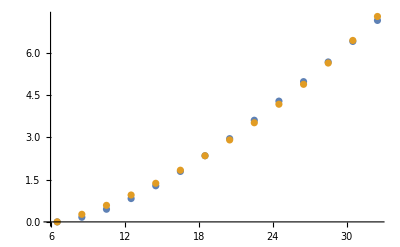

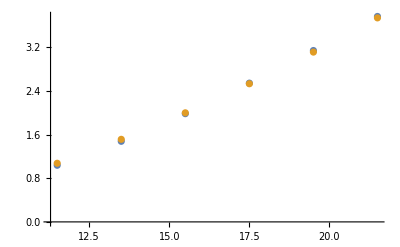

```mathematica
plotFunction[band_,params_,spins_,expData_]:=ListPlot[{Table[{spins[[i]],expData[[i]]},{i,1,Length[spins]}],Table[{spins[[i]],band[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{i,1,Length[spins]}]}];
plotFunction[band1Plus,paramSetPlus,s1Plus,yrastPlus]
plotFunction[band2Plus,paramSetPlus,s2Plus,tw1Plus]
```

## Plot data

## Test environment for the energy sub-terms

```mathematica
(*Table[Omega1[s1Plus[[i]],6.5,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]],{i,1,Length[s1Plus]}]
Table[Omega2[s1Plus[[i]],6.5,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]],{i,1,Length[s1Plus]}]
Table[B1[s1Plus[[i]],6.5,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]],{i,1,Length[s1Plus]}]
Table[C1[s1Plus[[i]],6.5,IF[params[[1]]],IF[params[[2]]],IF[params[[3]]],params[[4]],RAD[params[[5]]]],{i,1,Length[s1Plus]}]*)
```